1. Renormalization Group Recursive Equations Setup

```mathematica
Clear[μ,η,A,B,x0,x1,x2,x3,x4];
dim=8;
Clear[μ,η,y];
A[6]=B[6]=μ;
A[7]=B[7]=η;
y=1;
Z0[x0_,x1_,x2_,x3_,x4_]:=μ^(-(x0*x3+x1*x4+y*x0*x4)/2)*η^(-(x1+x3)/2)*Exp[-2*A[0]]*A[1]^(-((x0+x1)+(x1+x2)+(x2+x3)+(x3+x4))/2)*A[2]^(-((x0+x2)+(x2+x4))/2)*A[3]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/2)*A[4]^(-(x0*x2+x2*x4)/2)*A[5]^(-(x0*x1*x2+x2*x3*x4)/2)
Z1[x0_,x2_,x4_]:=Exp[-B[0]]*B[1]^(-((x0+x2)+(x2+x4))/2)*B[2]^(-(x0+x4)/2)*B[3]^(-(x0*x2+x2*x4)/2)*B[4]^(-(x0*x4)/2)*B[5]^(-x0*x2*x4/2)
TrZ0[x0_,x2_,x4_]:=Sum[Sum[Z0[x0,x1,x2,x3,x4],{x1,-1,1,2}],{x3,-1,1,2}]
i=0;
For[x0=-1,x0<=1,x0+=2,
For[x2=-1,x2<=1,x2+=2,
For[x4=-1,x4<=1,x4+=2,
leq[i]=Z1[x0,x2,x4];
req[i++]=TrZ0[x0,x2,x4];
]
]
]
(*Equates the unrenormalized with the renormalized variables*)
req[0]==leq[0];
req[1]==leq[1];
req[2]==leq[2];
req[3]==leq[3];
req[4] == leq[4];
req[5] ==leq[5] ;
req[6] ==leq[6] ;
req[7] ==leq[7] ;
SB[0]=Simplify[Solve[Simplify[(Factor[leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7]])^(-1/8),Assumptions->B[0]>0]==Simplify[(Factor[req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7]])^(-1/8),Assumptions->η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0],B[0]],Assumptions->C[1]==0&&η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0][[1]];
SB[0]={B[0]-> 2*A[0]+(B[0]/.SB[0]/.A[0]->0)};
SB[1]=Simplify[Part[Solve[Simplify[((leq[0]*leq[1]*leq[1]*leq[5])^(1/4)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0)]==Simplify[((req[0]*req[1]*req[1]*req[5])^(1/4)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[1]],1]];
SB[2]=Simplify[Part[Solve[Simplify[((leq[2]/leq[5]/leq[1])^(1/4)*(leq[0]/leq[1]*leq[2]*leq[3]*leq[4]/leq[5]*leq[6]/leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0&& B[2]>0&& B[4]>0&& B[5]>0)]==Simplify[((req[2]/req[5]/req[1])^(1/4)*(req[0]/req[1]*req[2]*req[3]*req[4]/req[5]*req[6]/req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[2]],1]];
SB[3]=Simplify[Part[Solve[Simplify[(leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->(B[0]>0 && B[3]>0)]==Simplify[(req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[3]],1]];
SB[4]=Simplify[Part[Solve[Simplify[(leq[1]*leq[3])/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->B[0]>0]==Simplify[(req[1]*req[3])/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[4]],1]];
SB[5]=Simplify[Part[Solve[Simplify[(leq[0]/leq[1]/leq[2]*leq[3])^(1/2)*((leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4)),Assumptions->(B[3]>0 && B[5]>0 && B[0]>0)]==Simplify[(req[0]/req[1]/req[2]*req[3])^(1/2)*((req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[5]],1]];
SBT=Table[Part[Factor[SB[n]],1],{n,0,5}];
```

2. Recursive Equation Setup

```mathematica
Clear[μ,η,A,B,x0,x1,x2,x,y,z,a,b,c]
Clear[μ,η]
y=1;
SIC={B[0]->0,B[1]->η,B[2]->η,B[3]->μ,B[4]->μ^(y),B[5]->1};
InitRG:=SAT=Table[A[n]->B[n]/.SIC,{n,0,dim-1}];
RG:=SAT=Table[A[n]->B[n]/.Simplify[SBT/.SAT],{n,0,dim-1}];
W=Table[Factor[D[(B[i]/.SBT),A[j]]],{j,0,dim-1},{i,0,dim-1}];
InitRGW:=Block[{},
InitRG;
Υ=Array[KroneckerDelta,{dim,dim}];
];
RGW:=Block[{},
Υ=Together[Υ.(W/.SAT)];
RG;
];
LnZ1=-A[0]+Log[Sum[Sum[Sum[η^(-(x0+x1+x2)/2)*A[1]^(-((x0+x1)+(x1+x2))/2)*A[2]^(-(x0+x2)/2)*A[3]^(-(x0*x1+x1*x2)/2)*A[4]^(-(x0*x2)/2)*A[5]^(-(x0*x1*x2)/2),{x0,-1,1,2}],{x1,-1,1,2}],{x2,-1,1,2}]];
LnZ1=-A[0]+(LnZ1/.A[0]->0);
DLnZ1=Table[Factor[D[LnZ1,A[i]]],{i,0,dim-1}];
InitRGW;
dμdβ=-4μ;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
Ω=Table[D[D[(B[j]/.SBT),A[i]],A[k]],{k,0,dim-1},{j,0,dim-1},{i,0,dim-1}];
InitRGΩ:=Block[{},
InitRGW;
Λ=0*Array[KroneckerDelta,{dim,dim,dim}];
(*Λ=Table[D[Υ,A[j]],{j,0,dim-1}];
This is all zero,anyway!*)
];
RGΩ:=Block[{},Λ=Together[Together[Λ.Together[W/.SAT]]+Transpose[Together[(Υ.Together[Ω/.SAT]).Transpose[Υ]],{1,3,2}]];
RGW;];
D2LnZ1=Factor[Table[D[DLnZ1,A[i]],{i,0,dim-1}]];
```

```mathematica
(* Free energy with fixed boundary: +1 x +1*)
Clear[μ,η,x0,x1,x2,x,y,z,a,b,c]
η=1;
LnZ1pp=-A[0]+Simplify[Log[Sum[Sum[Sum[η^(-(x0+x1+x2)/2)*A[1]^(-((x0+x1)+(x1+x2))/2)*A[2]^(-(x0+x2)/2)*A[3]^(-(x0*x1+x1*x2)/2)*A[4]^(-(x0*x2)/2)*A[5]^(-(x0*x1*x2)/2),{x0,1,1}],{x1,-1,1,2}],{x2,1,1}]]];
LnZ1mp=-A[0]+Simplify[Log[Sum[Sum[Sum[η^(-(x0+x1+x2)/2)*A[1]^(-((x0+x1)+(x1+x2))/2)*A[2]^(-(x0+x2)/2)*A[3]^(-(x0*x1+x1*x2)/2)*A[4]^(-(x0*x2)/2)*A[5]^(-(x0*x1*x2)/2),{x0,-1,-1}],{x1,-1,1,2}],{x2,1,1}]]];
LnZ1ratio=Simplify[Factor[LnZ1pp-LnZ1mp]]
LnZ1ratio2 = Factor[Log[(1+A[1]^2 A[3]^2 A[5])/(A[1]^2 A[2] A[3] √A[4] √A[5])/((√A[4] (A[1]^2+A[5]))/(A[1] √A[5]))]]
(*LnZ1ratio_real=Factor[LnZ1pp/LnZ1mp]*)
Ppp=Factor[Exp[-LnZ1pp]/(Exp[-LnZ1pp]+Exp[-LnZ1mp])];
Pmp=Factor[Exp[-LnZ1mp]/(Exp[-LnZ1pp]+Exp[-LnZ1mp])];
```

-Log[(√A[4] (A[1]^2+A[5]))/(A[1] √A[5])]+Log[(1+A[1]^2 A[3]^2 A[5])/(A[1]^2 A[2] A[3] √A[4] √A[5])]

Log[(1+A[1]^2 A[3]^2 A[5])/(A[1] A[2] A[3] A[4] (A[1]^2+A[5]))]

Analysis of free energy

Subdomain exploration T=0.13 ~ 0.60

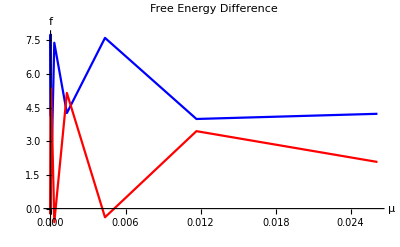

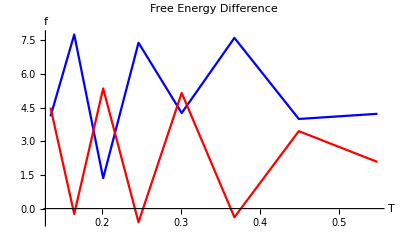

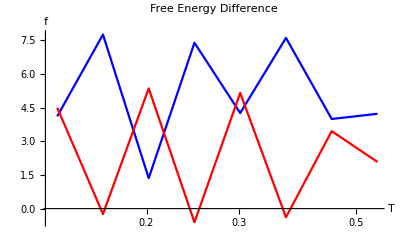

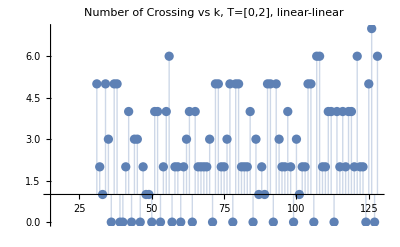

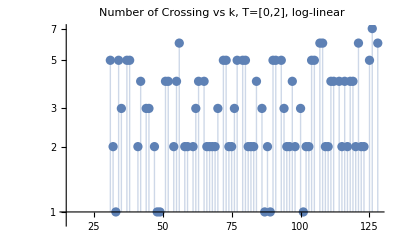

NcKs_31to128_T013to060_LogT.csv

freeEration_31to128_T013to060_LogT.csv

```mathematica
Clear[μ,η,freeEratio,kVectorc,FreeEcopy]
InitRGW;
precN=500;
logTmin=-2;
logTmax=-1/2;
logTinc=1/100000;
logTVector=Range[logTmin, logTmax,logTinc];
TVector=Exp[logTVector];
μVector=N[Exp[2/TVector],precN];
μinvVector=1/μVector;
kVector=Range[31,128,1];
InitRGW;
η=1;
freeEratio=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[TVector][[1]]}];
NcKs=ConstantArray[0,{Dimensions[kVector][[1]]}];
μind=0;
Do[kind=1;
μind++;
μ=N[μVector[[μind]],precN];
T=N[TVector[[μind]]];
InitRGW;
For[i=2,i≤Max[kVector],++i,RGW;
If[i==kVector[[kind]],
Part[Part[freeEratio,kind],μind]=N[2/Log[μ]*LnZ1ratio2/.SAT,precN];
NcKs[[kind]]=NcKs[[kind]]+If[μind>1&&(freeEratio[[kind]][[μind]]*freeEratio[[kind]][[μind-1]]<0.0|| freeEratio[[kind]][[μind]]==0.0),1,0];
kind++,
];
],
{Tx,1,Dimensions[μVector][[1]],1}
];
ListLinePlot[Table[Table[{1.0/μVector[[i]],freeEratio[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,Dimensions[kVector][[1]]-1,Dimensions[kVector][[1]]}],PlotRange->Full,PlotStyle->{Blue,Red,Orange,Cyan},PlotLabel->"Free Energy Difference",AxesLabel->{"μ", "f"}]
ListLinePlot[Table[Table[{TVector[[i]],freeEratio[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,Dimensions[kVector][[1]]-1,Dimensions[kVector][[1]]}],PlotRange->Full,PlotStyle->{Blue,Red,Orange,Cyan},PlotLabel->"Free Energy Difference",AxesLabel->{"T", "f"}]
ListLogLinearPlot[Table[Table[{TVector[[i]],freeEratio[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,Dimensions[kVector][[1]]-1,Dimensions[kVector][[1]]}],Joined->True,PlotRange->Full,PlotStyle->{Blue,Red,Orange,Cyan},PlotLabel->"Free Energy Difference",AxesOrigin->{Tmin,0},AxesLabel->{"T", "f"}]
ListPlot[Table[{kVector[[i]],NcKs[[i]]},{i,1,Dimensions[kVector][[1]]}],Filling->Axis,AxesOrigin->{15,1},PlotLabel->"Number of Crossing vs k, T=[0,2], linear-linear"]
ListLogPlot[Table[{kVector[[i]],NcKs[[i]]},{i,1,Dimensions[kVector][[1]]}],Filling->Axis,AxesOrigin->{15,1},PlotLabel->"Number of Crossing vs k, T=[0,2], log-linear"]

kVectorc=kVector;
Export["NcKs_31to128_T013to060_LogT.csv",Transpose[{kVectorc, NcKs}]]
FreeEcopy=N[freeEratio,10];
FreeEcopy=PrependTo[FreeEcopy,N[TVector,10]];
FreeEcopy=PrependTo[FreeEcopy,N[μinvVector,10]];
kVectorc=PrependTo[kVectorc,0];
kVectorc=PrependTo[kVectorc,0];
FreeEcopy=Transpose[FreeEcopy];
FreeEcopy=PrependTo[FreeEcopy,kVectorc];
Export["freeEration_31to128_T013to060_LogT.csv",FreeEcopy]
```

```mathematica
Subdomain exploration T= 0.9Tg~Tg
```

NcKs_63to128_T09TgtoTg_LinearT.csv

General::aofil: "/home/xcheng0907/freeEration_63to128_T09TgtoTg_LinearT.csv" already open as "/home/xcheng0907/freeEration_63to128_T09TgtoTg_LinearT.csv".

OpenWrite::noopen: Cannot open "/home/xcheng0907/freeEration_63to128_T09TgtoTg_LinearT.csv".

$Failed

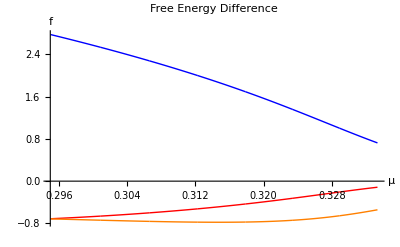

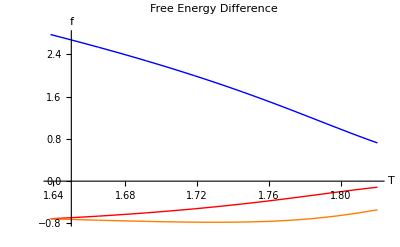

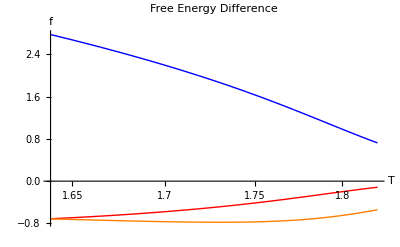

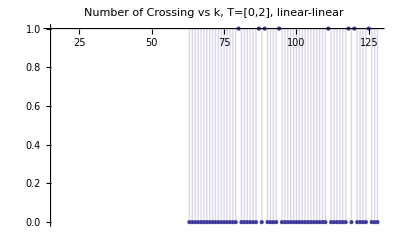

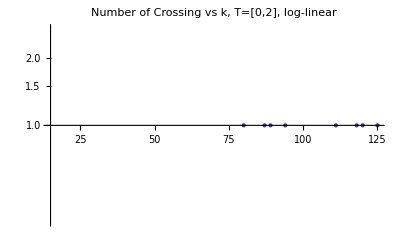

```mathematica
Clear[μ,η,freeEratio,freeEratio2,freeEcopy]
InitRGW;
(**Temperature for Mag, IE**)
precN=500;
Tmin=2/Log[3]*9/10;
Tmax=2/Log[3];
Tinc=1/300000;
TVector=Range[Tmin, Tmax,Tinc];
μVector=N[Exp[2/TVector],precN];
μinvVector=1/μVector;
kVector=Range[63,128,1];
InitRGW;
η=1;
freeEratio=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[TVector][[1]]}];
NcKs=ConstantArray[0,{Dimensions[kVector][[1]]}];
μind=0;
Do[kind=1;
μind++;
μ=N[μVector[[μind]],precN];
T=N[TVector[[μind]]];
InitRGW;
For[i=2,i≤Max[kVector],++i,RGW;
If[i==kVector[[kind]],
Part[Part[freeEratio,kind],μind]=N[2/Log[μ]*LnZ1ratio2/.SAT,precN];
NcKs[[kind]]=NcKs[[kind]]+If[μind>1&&(freeEratio[[kind]][[μind]]*freeEratio[[kind]][[μind-1]]<0.0|| freeEratio[[kind]][[μind]]==0.0),1,0];
kind++,
];
],
{Tx,1,Dimensions[μVector][[1]],1}
];
kVectorc=kVector;
Export["NcKs_63to128_T09TgtoTg_LinearT.csv",Transpose[{kVectorc, NcKs}]]
FreeEcopy=N[freeEratio,10];
FreeEcopy=PrependTo[FreeEcopy,N[TVector,10]];
FreeEcopy=PrependTo[FreeEcopy,N[μinvVector,10]];
kVectorc=PrependTo[kVectorc,0];
kVectorc=PrependTo[kVectorc,0];
FreeEcopy=Transpose[FreeEcopy];
FreeEcopy=PrependTo[FreeEcopy,kVectorc];
Export["freeEration_63to128_T09TgtoTg_LinearT.csv",FreeEcopy]

ListLinePlot[Table[Table[{1.0/μVector[[i]],freeEratio[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,Dimensions[kVector][[1]]-2,Dimensions[kVector][[1]]}],PlotRange->Full,PlotStyle->{Blue,Red,Orange,Cyan},PlotLabel->"Free Energy Difference",AxesLabel->{"μ", "f"}]
ListLinePlot[Table[Table[{TVector[[i]],freeEratio[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,Dimensions[kVector][[1]]-2,Dimensions[kVector][[1]]}],PlotRange->Full,PlotStyle->{Blue,Red,Orange,Cyan},PlotLabel->"Free Energy Difference",AxesLabel->{"T", "f"}]
ListLogLinearPlot[Table[Table[{TVector[[i]],freeEratio[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,Dimensions[kVector][[1]]-2,Dimensions[kVector][[1]]}],Joined->True,PlotRange->Full,PlotStyle->{Blue,Red,Orange,Cyan},PlotLabel->"Free Energy Difference",AxesOrigin->{Tmin,0},AxesLabel->{"T", "f"}]
ListPlot[Table[{kVector[[i]],NcKs[[i]]},{i,1,Dimensions[kVector][[1]]}],Filling->Axis,AxesOrigin->{15,1},PlotLabel->"Number of Crossing vs k, T=[0,2], linear-linear"]
ListLogPlot[Table[{kVector[[i]],NcKs[[i]]},{i,1,Dimensions[kVector][[1]]}],Filling->Axis,AxesOrigin->{15,1},PlotLabel->"Number of Crossing vs k, T=[0,2], log-linear"]
```

```mathematica
kVectorc=kVector;
Export["NcKs_63to128_T09TgtoTg_LinearT.csv",Transpose[{kVectorc, NcKs}]]
FreeEcopy=N[freeEratio,10];
FreeEcopy=PrependTo[FreeEcopy,N[TVector,10]];
FreeEcopy=PrependTo[FreeEcopy,N[μinvVector,10]];
kVectorc=PrependTo[kVectorc,0];
kVectorc=PrependTo[kVectorc,0];
FreeEcopy=Transpose[FreeEcopy];
FreeEcopy=PrependTo[FreeEcopy,kVectorc];
Export["abc.csv",FreeEcopy]
```

NcKs_63to128_T09TgtoTg_LinearT.csv

abc.csv

```mathematica
Dimensions[FreeEcopy]
```

{54616,68}